Solucion exacta

6.5-20.6 x+12.5 x^2-2 x^3

1+6.5 x-10.3 x^2+4.16667 x^3-x^4/2

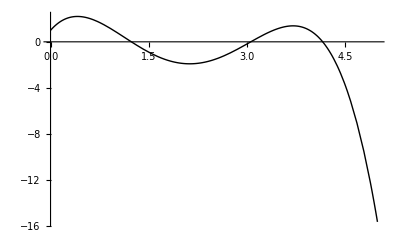

```mathematica
(*Solución exacta*)
Print["Solucion exacta"]
f[x_]=-2 x^3+12.5 x^2-20.6 x+6.5
F[x_]=6.5 x-10.3 x^2+4.166666666666666 x^3-x^4/2+1
grafica1=Plot[F[x],{x,0,5},PlotRange->All,PlotStyle->Directive[Black,PointSize[Large]]]
```

```mathematica
6.5-20.6 x+12.5 x^2-2 x^3
```

6.5-20.6 x+12.5 x^2-2 x^3

Euler

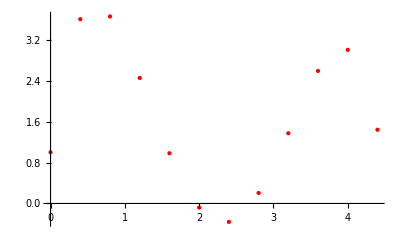

Pmedio

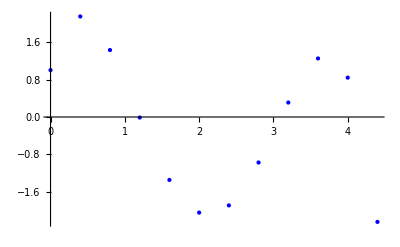

Heun

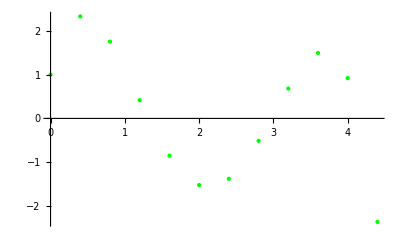

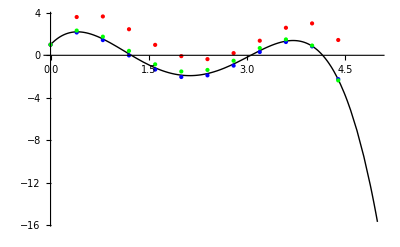

```mathematica
(*Metodo de Euler*)
Print["Euler"]
x0=0;
y0=1;
h=0.4;
xf=5;
f[x_,y_]=-2 x^3+12.5 x^2-20.6 x+6.5;
(*f[x_,y_]=-Sin[x^2]Exp[y];*)
n=(xf-x0)/h;

lasx={};
AppendTo[lasx,x0];
For[i=2,i≤n,i++,
aux=x0+h (i-1);
AppendTo[lasx,aux]
]
lasx;

lasy={};
AppendTo[lasy,y0];
For[i=2,i≤n,i++,
aux=lasy[[i-1]]+f[lasx[[i-1]],lasy[[i-1]]]h ;
AppendTo[lasy,aux]
]

datos1=Table[{lasx[[i]],lasy[[i]]},{i,1,n}];
grafica2=ListPlot[datos1,(*Joined->True,*)PlotRange->All,PlotStyle->Directive[Red,PointSize[Large]]]

Print["Pmedio"]
lasx={};
AppendTo[lasx,x0];
For[i=2,i≤n,i++,
aux=x0+h (i-1);
AppendTo[lasx,aux]
]
lasx;

lasy={};
AppendTo[lasy,y0];
For[i=2,i≤n,i++,
k1=f[lasx[[i-1]],lasy[[i-1]]];
ymed=lasy[[i-1]]+k1 h/2;
xmed=lasx[[i-1]]+ h/2;
k2=f[xmed,ymed];

aux=lasy[[i-1]]+k2 h ;
AppendTo[lasy,aux]
]

datos2=Table[{lasx[[i]],lasy[[i]]},{i,1,n}];
grafica3=ListPlot[datos2,(*Joined->True,*)PlotRange->All,PlotStyle->Directive[Blue,PointSize[Large]]]

Print["Heun"]

lasx={};
AppendTo[lasx,x0];
For[i=2,i≤n,i++,
aux=x0+h (i-1);
AppendTo[lasx,aux]
]

lasy={};
AppendTo[lasy,y0];
For[i=2,i≤n,i++,
k1=f[lasx[[i-1]],lasy[[i-1]]];
auxy=lasy[[i-1]]+k1 h;
auxx=lasx[[i-1]]+h;

k2=f[auxx,auxy];
aux=lasy[[i-1]]+((k1+k2)/2) h;
AppendTo[lasy,aux]
]

datos3=Table[{lasx[[i]],lasy[[i]]},{i,1,n}];
grafica4=ListPlot[datos3,(*Joined->True,*)PlotRange->All,PlotStyle->Directive[Green,PointSize[Large]]]


Show[grafica1,grafica2,grafica3,grafica4]
```